```mathematica
(*pokličemo zunanje funkcije*)
```

```mathematica
Get["C:\\Adam\\FAKS\\3.letnik\\1.semester\\NAPREDNA RAČUNALNIŠKA ORODJA\\DN2\\Generacija_tock.m"]
```

```mathematica
Get["C:\\Adam\\FAKS\\3.letnik\\1.semester\\NAPREDNA RAČUNALNIŠKA ORODJA\\DN2\\LocevanjeSeznamov.m"]
```

```mathematica
seznamvseh = GeneracijaTock[100000]; (*ustvarimo seznam*)
```

```mathematica
{notri,zunaj}=LocevanjeSeznamov[seznamvseh]; (*ločimo seznama*)
```

```mathematica
(*pogledamo, koliko elementov ima vsak seznam*)
```

```mathematica
stvseh=Length[seznamvseh];
n=Length[notri];
z=Length[zunaj];
```

```mathematica
(*izračunamo pi*)
```

```mathematica
SteviloPI=N[ (4 n)/stvseh]
```

3.14192

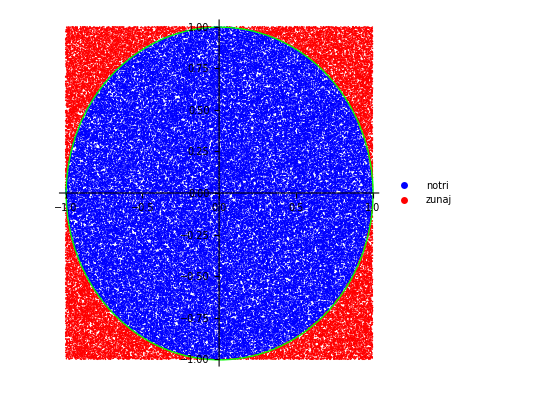

```mathematica
(*grafični prikaz*)
p1=ListPlot[{notri},PlotStyle->Blue,AspectRatio->1,PlotRange->{{-1,1},{-1,1}},PlotLegends->{"notri"}];
p2=ListPlot[{zunaj},PlotStyle->Red,PlotLegends->{"zunaj"}];
p3=Graphics[{EdgeForm[Black],FaceForm[None],Green,Circle[{0,0},1]},Axes->True,AspectRatio->1,PlotRange->{{-1,1},{-1,1}}];
Show[p1,p2,p3,PlotRange->{{-1,1},{-1,1}}]
```